# Transfer Learning with Invertible Neural Networks

Joshua Pedro

Etienne Bernard and Jerome Louradour

## Dataset

Given a set of grayscale images of handwritten digits (28×28 pixels) from zero to eight, can we train a neural network to first learn the distribution from which these images can be generated? Can we then try to use this network to generate the digit nine from a small number of examples? For this task, we’ll use the classic MNIST dataset which consists of 60000 training images.

First we import the data from the Wolfram Data Repository:

```mathematica
mnist=ResourceData["MNIST"][[All,1]];
```

```mathematica
mnistplot=RandomSample[mnist,90];
```

```mathematica
FeatureSpacePlot[Join[RandomSample[digits08,90],gen9],LabelingSize->15,PerformanceGoal->"Quality"]
```

-Graphics-

Extract from this dataset only the examples with digits from 0 to 8:

```mathematica
digits08=Cases[ResourceData["MNIST"],Except[_->9]][[All,1]];
```

```mathematica
Export["image1.gif",Table[RandomSample[digits08,10],10],AnimationRepetitions->Infinity]
```

image1.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["image1.gif"]]]
```

## Transfer Learning

We would like to use features already learned in our model to generate a good representation of the digit nine. Note that our model has not yet seen the digit nine, so by transfer learning, we will give our model only 10 examples of nines to see how well it can generate them.

### New data and model

Import data with the digit 9 only :

```mathematica
digit9=Cases[ResourceData["MNIST"],HoldPattern[_->9]] ⟦All,1⟧;
```

Now we only take 10 examples to train the model on:

```mathematica
sampledigit9=RandomSample[digit9,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}
```

```mathematica
Export["image4.gif",Table[RandomSample[digit9,10],10],AnimationRepetitions->Infinity]
```

image4.gif

Finally, we train the model but this time using the Multinormal method :

```mathematica
ld9=LearnDistribution[sampledigit9,Method->{"Multinormal","IntrinsicDimension"->10,"CovarianceType"->"Diagonal"},PerformanceGoal->"Quality"];
```

```mathematica
RandomVariate[ld9,10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ld9[[1,"Model","Sampler"]]
```

Missing[KeyAbsent,Sampler]

```mathematica
Export["image6.gif",Table[RandomVariate[ld9,10],20],AnimationRepetitions->Infinity]
```

image6.gif

```mathematica
SystemOpen["image6.gif"]
```

Finally, we train the model but this time using the RealNVP method :

```mathematica
ld9test=LearnDistribution[sampledigit9,Method->{"RealNVP","NetworkDepth"->4,"CouplingLayersNumber"->4,MaxTrainingRounds->40,"ActivationFunction"->Ramp},PerformanceGoal->"DirectTraining"]
```

LearnedDistribution[…]

```mathematica
Export["image5.gif",Table[RandomVariate[ld9test,10],10],AnimationRepetitions->Infinity]
```

image5.gif

```mathematica
SystemOpen["image5.gif"]
```

```mathematica
Export["image5.gif",RandomVariate[ld9test,10]]
```

image5.gif

### Data space → Latent space

```mathematica
checkeredGen[inpdim_, checkeredType_, mreplicat_] := Module[
	{resLayer, replayer, checkerf},
	replayer = ReplicateLayer[mreplicat];
	checkerf = If[Depth@inpdim > 1,
		resLayer = ReshapeLayer[inpdim];
		{Normal@SparseArray[{{i_, j_}/; Switch[checkeredType, "black", OddQ[i + j], "white", EvenQ[i + j]] == True -> 1}, inpdim]},
		resLayer = ReshapeLayer[{inpdim}];
		{Normal@SparseArray[{{i_}/; Switch[checkeredType, "black", OddQ[i], "white", EvenQ[i]] == True -> 1}, inpdim]}
		];
	checkerf = resLayer@checkerf;
	Normal[replayer[checkerf]]
]
```

```mathematica
pp=ldtrial4⟦1,"Preprocessor"⟧;
p=ldtrial4⟦1,"Processor"⟧;
mpr=ldtrial4⟦1, "Model", "Processor"⟧;
mppr=ldtrial4⟦1, "Model", "PostProcessor"⟧;
```

```mathematica
trainednet=ldtrial4⟦1,"Model","ProbabilityNet"⟧
```

NetGraph[<>]

```mathematica
sampler=ldtrial4⟦1,"Model","Sampler"⟧
```

NetGraph[<>]

```mathematica
nn=trainednet⟦"Input"⟧;
mm=Length@sampledigit9
```

10

```mathematica
{mm,nn}=Dimensions@mppr[p[pp[sampledigit9]]]
```

{10,784}

```mathematica
checkerW=checkeredGen[nn, "white", mm];
checkerB=checkeredGen[nn, "black", mm];
```

```mathematica
Dimensions@checkerW
```

{10,784}

#### Mapping to Latent Space (X→Z)

```mathematica
z9=trainednet[<|"Input"->mppr[mpr[p[pp[sampledigit9]]]], "checker_w"-> checkerW, "checker_b"-> checkerB|>][["Z_out"]];
```

#### Learn distribution

```mathematica
ld9=LearnDistribution[z9,Method->{"Multinormal","IntrinsicDimension"->10,"CovarianceType"->"Diagonal"},PerformanceGoal->"Quality"];
```

```mathematica
sampledz=RandomVariate[ld9,10];
```

```mathematica
pp[p[mpr[mppr[sampler[<|"Input"->RandomVariate[ld9,10],"checker_w"->checkerW,"checker_b"->checkerB|>],"Inverse"],"Inverse"],"Inverse"],"Inverse"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
gen9={-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-};
```

```mathematica
Export["image6.gif",Table[pp[p[mpr[mppr[sampler[<|"Input"->RandomVariate[ld9,10],"checker_w"->checkerW,"checker_b"->checkerB|>],"Inverse"],"Inverse"],"Inverse"],"Inverse"],10],AnimationRepetitions->Infinity]
```

image6.gif

```mathematica
SystemOpen["image6.gif"]
```

#### Generation (Z→X)

```mathematica
inputdim=sampler[["Input"]]
n=10;
xgen=RandomVariate[NormalDistribution[0,1],{n,inputdim}];
checkerW=checkeredGen[inputdim,"white",n];
checkerB=checkeredGen[inputdim,"black",n];
```

784

```mathematica
samples=sampler[<|"Input"->xgen,"checker_w"->checkerW,"checker_b"->checkerB|>];
```

```mathematica
pp[p[mpr[mppr[samples,"Inverse"],"Inverse"],"Inverse"],"Inverse"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Transformation

### Data space → Latent space

```mathematica
sampledigit2=RandomSample[Cases[ResourceData["MNIST"],HoldPattern[_->2]]⟦All,1⟧,1]
```

{-Graphics-}

```mathematica
sampledigit8=RandomSample[Cases[ResourceData["MNIST"],HoldPattern[_->8]]⟦All,1⟧,1]
```

{-Graphics-}

### 2→Z

```mathematica
nn=trainednet⟦"Input"⟧
mm=Length@sampledigit2
```

784

1

```mathematica
{mm,nn}=Dimensions@mppr[p[pp[sampledigit2]]]
```

{1,784}

```mathematica
checkerW=checkeredGen[nn, "white", mm];
checkerB=checkeredGen[nn, "black", mm];
```

```mathematica
Dimensions@checkerW
```

{1,784}

#### Mapping to Latent Space (2→Z)

```mathematica
z[digit_]:=Module[
{nn,mm,checkerW,checkerB},
	nn = trainednet⟦"Input"⟧
```

```mathematica
z2=trainednet[<|"Input"->mppr[mpr[p[pp[sampledigit2]]]], "checker_w"-> checkerW, "checker_b"-> checkerB|>][["Z_out"]];
```

#### Generation (Z→2)

```mathematica
inputdim=sampler[["Input"]];
n=1;
xgen=RandomVariate[NormalDistribution[0,1],{n,inputdim}];
checkerW=checkeredGen[inputdim,"white",n];
checkerB=checkeredGen[inputdim,"black",n];
```

```mathematica
samples=sampler[<|"Input"->xgen,"checker_w"->checkerW,"checker_b"->checkerB|>];
```

```mathematica
pp[p[mpr[mppr[samples,"Inverse"],"Inverse"],"Inverse"],"Inverse"]
```

{-Graphics-}

### 8→Z

```mathematica
nn=trainednet⟦"Input"⟧;
mm=Length@sampledigit8
```

1

```mathematica
{mm,nn}=Dimensions@mppr[p[pp[sampledigit8]]]
```

{1,784}

```mathematica
checkerW=checkeredGen[nn, "white", mm];
checkerB=checkeredGen[nn, "black", mm];
```

```mathematica
Dimensions@checkerW
```

{1,784}

#### Mapping to Latent Space (8→Z)

```mathematica
z8=trainednet[<|"Input"->mppr[mpr[p[pp[sampledigit8]]]], "checker_w"-> checkerW, "checker_b"-> checkerB|>][["Z_out"]];
```

### Parameterization

```mathematica
f[t_]:=(1-t)z2+t z8
```

### Generation (Z→2)

```mathematica
inputdim=sampler[["Input"]];
n=1;
xgen=RandomVariate[NormalDistribution[0,1],{n,inputdim}];
checkerW=checkeredGen[inputdim,"white",n];
checkerB=checkeredGen[inputdim,"black",n];
```

```mathematica
samples=sampler[<|"Input"->xgen,"checker_w"->checkerW,"checker_b"->checkerB|>];
```

```mathematica
pp[p[mpr[mppr[samples,"Inverse"],"Inverse"],"Inverse"],"Inverse"]⟦1⟧
```

{-Graphics-}

```mathematica
samples=sampler[<|"Input"->z2,"checker_w"->checkerW,"checker_b"->checkerB|>];
```

```mathematica
Manipulate[pp[p[mpr[mppr[sampler[<|"Input"->f[t],"checker_w"->checkerW,"checker_b"->checkerB|>],"Inverse"],"Inverse"],"Inverse"],"Inverse"],{t,0,1}]
```

NetGraph::invindata2: Data supplied to port "checker_b" was not a length-784 vector of real numbers (or a list of these).

Partition::pdep: Depth 1 requested in object with dimensions {}.

Image::imgarray: The specified argument 256 Partition[$Failed,28] should be an array of rank 2 or 3 with machine-sized numbers.

NetGraph::invindata2: Data supplied to port "checker_b" was not a length-784 vector of real numbers (or a list of these).

Partition::pdep: Depth 1 requested in object with dimensions {}.

Image::imgarray: The specified argument 256 Partition[$Failed,28] should be an array of rank 2 or 3 with machine-sized numbers.

NetGraph::enetragged: When evaluating batches of inputs, all input ports must be given lists of the same length.

Partition::pdep: Depth 1 requested in object with dimensions {}.

Image::imgarray: The specified argument 256 Partition[$Failed,28] should be an array of rank 2 or 3 with machine-sized numbers.

NetGraph::invindata2: Data supplied to port "checker_b" was not a length-784 vector of real numbers (or a list of these).

Partition::pdep: Depth 1 requested in object with dimensions {}.

Image::imgarray: The specified argument 256 Partition[$Failed,28] should be an array of rank 2 or 3 with machine-sized numbers.

NetGraph::invindata2: Data supplied to port "checker_b" was not a length-784 vector of real numbers (or a list of these).

Partition::pdep: Depth 1 requested in object with dimensions {}.

Image::imgarray: The specified argument 256 Partition[$Failed,28] should be an array of rank 2 or 3 with machine-sized numbers.

NetGraph::invindata2: Data supplied to port "checker_b" was not a length-2 vector of real numbers (or a list of these).

```mathematica
Animate[Flatten@pp[p[mpr[mppr[sampler[<|"Input"->f[t],"checker_w"->checkerW,"checker_b"->checkerB|>],"Inverse"],"Inverse"],"Inverse"],"Inverse"],{t,0,1},SaveDefinitions->True]
```

$Aborted[]

# Appendix

## Training

For training on the dataset, we use LearnDistribution[] which will attempt to understand the underlying distribution for the given data. The method used will be RealNVP for which we will attempt four different hyper-parameter configurations. We will then select the best model to perform our transfer learning task.

We use LearnDistribution[] to train on MNIST digits 0 to 8 by the RealNVP technique:

```mathematica
ld08=LearnDistribution[digits08,Method->{"RealNVP","NetworkDepth"->4,"CouplingLayersNumber"->2,MaxTrainingRounds->100,"ActivationFunction"->Ramp},PerformanceGoal->"DirectTraining"]
```

### Training Results

#### Model 1: depth=2, coupling=2, activation=Ramp

```mathematica
trial1=SemanticImport["E:\\train\\TrainedDistributionMNIST0-8_depth2_coupling2_nonlinRamp\\traininglog.csv"]
```

Dataset[<>]

```mathematica
ListPlot[trial1⟦{2},{10}⟧]
```

-Graphics-

##### Model

```mathematica
ldtrial1=Import["D:\\train\\TrainedDistributionMNIST0-8_depth2_coupling2_nonlinRamp\\model.mx"];
```

```mathematica
RandomVariate[ldtrial1,40]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Model 2: depth=4, coupling=2, activation=Ramp

```mathematica
trial2=SemanticImport["E:\\train\\TrainedDistributionMNIST0-8_depth4_coupling2_nonlinRamp\\traininglog.csv"]
```

Dataset[<>]

##### Model

```mathematica
ldtrial2=Import["D:\\train\\TrainedDistributionMNIST0-8_depth4_coupling2_nonlinRamp\\model.mx"];
```

```mathematica
RandomVariate[ldtrial2,40]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Model 3: depth=4, coupling=2, activation=Tanh, L2Regularization

```mathematica
trial3=SemanticImport["E:\\train\\TrainedDistributionMNIST0-8_depth4_coupling2_nonlinTanh_L2-5e-5\\traininglog.csv"]
```

Dataset[<>]

##### Model

```mathematica
ldtrial3=Import["D:\\train\\TrainedDistributionMNIST0-8_depth4_coupling2_nonlinTanh_L2-5e-5\\model.mx"];
```

```mathematica
RandomVariate[ldtrial3,40]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Model 4: depth=4, coupling=4, activation=Ramp

```mathematica
trial4=SemanticImport["D:\\train\\TrainedDistributionMNIST0-8_depth4_coupling4_nonlinRamp\\traininglog.csv"]
```

Dataset[<>]

##### Model

```mathematica
ldtrial4=Import["D:\\train\\TrainedDistributionMNIST0-8_depth4_coupling4_nonlinRamp\\model.mx"];
```

```mathematica
NetInformation[ldtrial4⟦1,"Model","ProbabilityNet"⟧,"MXNetNodeGraph"]
```

```mathematica
Grid[{RandomVariate[ldtrial4,10],RandomVariate[ldtrial4,10],RandomVariate[ldtrial4,10],RandomVariate[ldtrial4,10]}]
```

-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Export["image2.gif",%]
```

image2.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["image2.gif"]]]
```

```mathematica
SystemOpen["image2.gif"]
```

#### Summary of Training Results

```mathematica
ListLinePlot[{trial1⟦All,{2,10}⟧,trial2⟦All,{2,10}⟧,trial3⟦All,{2,10}⟧,trial4⟦All,{2,10}⟧},AxesLabel->Automatic,PlotLegends->{"Model 1","Model 2","Model 3","Model 4"},PlotLabel->"Loss"]
```

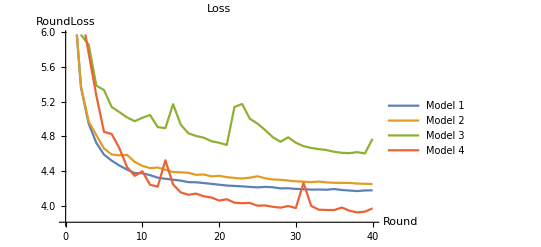
```mathematica
Export["image3.gif",-Graphics-]
```

image3.gif

```mathematica
SystemOpen["image3.gif"]
```

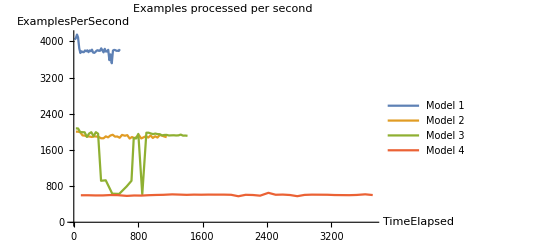

```mathematica
BarChart[{Median[trial1⟦All,{7,5}⟧],Median[trial2⟦All,{7,5}⟧],Median[trial3⟦All,{7,5}⟧],Median[trial4⟦All,{7,5}⟧]},AxesLabel->Automatic,PlotLabel->"Examples processed per second"]
```

#### Graphic

```mathematica
digit9=Cases[ResourceData["MNIST"],HoldPattern[_->9]] ⟦All,1⟧;
digit8=Cases[ResourceData["MNIST"],HoldPattern[_->8]] ⟦All,1⟧;
digit7=Cases[ResourceData["MNIST"],HoldPattern[_->7]] ⟦All,1⟧;
digit6=Cases[ResourceData["MNIST"],HoldPattern[_->6]] ⟦All,1⟧;
digit5=Cases[ResourceData["MNIST"],HoldPattern[_->5]] ⟦All,1⟧;
digit4=Cases[ResourceData["MNIST"],HoldPattern[_->4]] ⟦All,1⟧;
digit3=Cases[ResourceData["MNIST"],HoldPattern[_->3]] ⟦All,1⟧;
digit2=Cases[ResourceData["MNIST"],HoldPattern[_->2]] ⟦All,1⟧;
digit1=Cases[ResourceData["MNIST"],HoldPattern[_->1]] ⟦All,1⟧;
digit0=Cases[ResourceData["MNIST"],HoldPattern[_->0]] ⟦All,1⟧;
```

```mathematica
FeatureSpacePlot[Join[RandomSample[digit0,10],RandomSample[digit1,10],RandomSample[digit2,10],RandomSample[digit3,10],RandomSample[digit4,10],RandomSample[digit5,10],RandomSample[digit6,10],RandomSample[digit7,10],RandomSample[digit8,10],RandomSample[digit9,10]]]
```

-Graphics-

```mathematica
FeatureSpacePlot[Join[RandomVariate[ldtrial4,90],gen9]]
```

-Graphics-

```mathematica
Export["summary2.gif",-Graphics-->-Graphics-]
```

summary2.gif

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["summary2.gif"]]]
```